## One Trem

```mathematica
oneTerm:=Block[{m,n,α,β},
{m,n}=RandomInteger[{-6,6},2];
{α,β}=Rationalize[RandomReal[{-π,π},2],1/1000];
RandomReal[{-1,1}]{m Cos[n x+α]Cos[m y+β],n Sin[n x+α]Sin[m y+β]}
];
uv=Sum[oneTerm,{6}]
```

{-5 Cos[59/22+3 x] Cos[71/53-5 y]-4 Cos[25/18+3 x] Cos[9/14-4 y]-3 Cos[49/37+4 x] Cos[23/25-3 y]-3 Cos[25/28-6 x] Cos[45/17-3 y]-6 Cos[82/35] Cos[12/43+6 y]-6 Cos[43/14+5 x] Cos[37/22+6 y],3 Sin[59/22+3 x] Sin[71/53-5 y]+3 Sin[25/18+3 x] Sin[9/14-4 y]+4 Sin[49/37+4 x] Sin[23/25-3 y]-6 Sin[25/28-6 x] Sin[45/17-3 y]-5 Sin[43/14+5 x] Sin[37/22+6 y]}

## Analysis

```mathematica
<<MathPrintF`
readh5[pth_,i_]:=Module[{ds,uvs},
ds=Import[pth,{"Datasets",sprintf["/%03d/c",i]}];
uvs=RunProcess[{"/Users/yohai/anaconda2/bin/python","-c",sprintf["import h5py; print h5py.File('/%s')['/%03d'].attrs['vu_MMA']",pth,i]}]["StandardOutput"];
(*uvs=Block[{u,v},ToExpression@*)
uvs=ToExpression[StringDrop[StringReplace[uvs,{"u="->"{","; v="->","}],-2]<>"}"];
{ds,uvs}
]
```

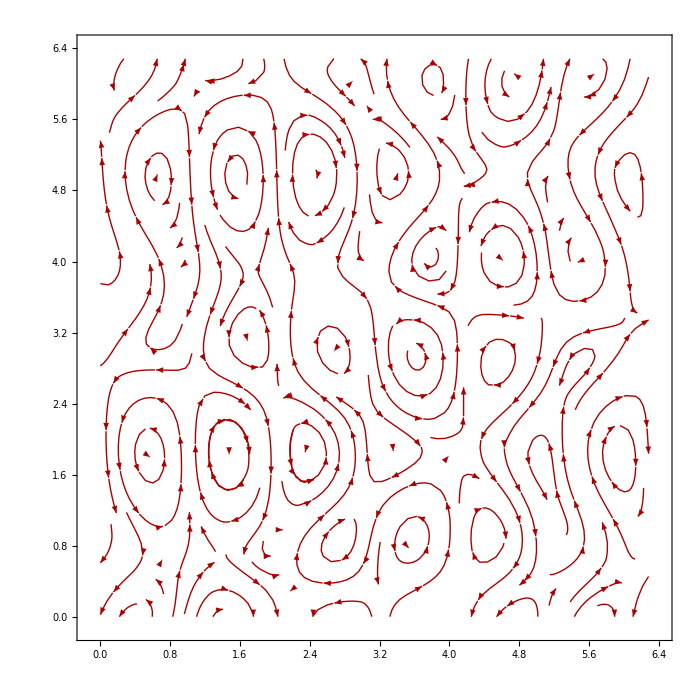

```mathematica
{ds,ff}=readh5["/Volumes/ybarsinai/advection-diffusion/data/4.6e-02.h5",13];
gs=StreamPlot[Evaluate@ff,{x,0,2π},{y,0,2π},StreamPoints->3000,PlotRangePadding->None,StreamStyle->Darker[Red],ImageSize->700,VectorStyle->Arrowheads[0]]
```

```mathematica
.
```

```mathematica
Manipulate[Show[ReliefPlot[ds⟦All,All,i⟧ᵀ,PlotRange->MinMax[ds],DataRange->{{0,2π},{0,2π}}],gs,PlotRange->{{0,2π},{0,2π}},ImageSize->700],{i,1,Length@ds,1}]
```

```mathematica
Dimensions@ds⟦All,All,1⟧
```

{200,200}

```mathematica
sprintf["import h5py; print h5py.File('/%s')['/%03d'].attrs['vu_MMA']","/Volumes/ybarsinai/advection-diffusion/data/1.0e-03.h5",24]
```

import h5py; print h5py.File('//Volumes/ybarsinai/advection-diffusion/data/1.0e-03.h5')['/024'].attrs['vu_MMA']

```mathematica
Table[Export[sprintf["~/tmp/a/b%03d.png",i],Show[ReliefPlot[ds⟦All,All,i⟧ᵀ,PlotRange->MinMax[ds],DataRange->{{0,2π},{0,2π}}],gs,PlotRange->{{0,2π},{0,2π}},ImageSize->700]],{i,1,Last@Dimensions@ds,1}]
```

{~/tmp/a/b001.png,~/tmp/a/b002.png,~/tmp/a/b003.png,~/tmp/a/b004.png,~/tmp/a/b005.png,~/tmp/a/b006.png,~/tmp/a/b007.png,~/tmp/a/b008.png,~/tmp/a/b009.png,~/tmp/a/b010.png,~/tmp/a/b011.png,~/tmp/a/b012.png,~/tmp/a/b013.png,~/tmp/a/b014.png,~/tmp/a/b015.png,~/tmp/a/b016.png,~/tmp/a/b017.png,~/tmp/a/b018.png,~/tmp/a/b019.png,~/tmp/a/b020.png,~/tmp/a/b021.png,~/tmp/a/b022.png,~/tmp/a/b023.png,~/tmp/a/b024.png,~/tmp/a/b025.png,~/tmp/a/b026.png,~/tmp/a/b027.png,~/tmp/a/b028.png,~/tmp/a/b029.png,~/tmp/a/b030.png,~/tmp/a/b031.png,~/tmp/a/b032.png,~/tmp/a/b033.png,~/tmp/a/b034.png,~/tmp/a/b035.png,~/tmp/a/b036.png,~/tmp/a/b037.png,~/tmp/a/b038.png,~/tmp/a/b039.png,~/tmp/a/b040.png,~/tmp/a/b041.png,~/tmp/a/b042.png,~/tmp/a/b043.png,~/tmp/a/b044.png,~/tmp/a/b045.png,~/tmp/a/b046.png,~/tmp/a/b047.png,~/tmp/a/b048.png,~/tmp/a/b049.png,~/tmp/a/b050.png,~/tmp/a/b051.png,~/tmp/a/b052.png,~/tmp/a/b053.png,~/tmp/a/b054.png,~/tmp/a/b055.png,~/tmp/a/b056.png,~/tmp/a/b057.png,~/tmp/a/b058.png,~/tmp/a/b059.png,~/tmp/a/b060.png,~/tmp/a/b061.png,~/tmp/a/b062.png,~/tmp/a/b063.png,~/tmp/a/b064.png,~/tmp/a/b065.png,~/tmp/a/b066.png,~/tmp/a/b067.png,~/tmp/a/b068.png,~/tmp/a/b069.png,~/tmp/a/b070.png,~/tmp/a/b071.png,~/tmp/a/b072.png,~/tmp/a/b073.png,~/tmp/a/b074.png,~/tmp/a/b075.png,~/tmp/a/b076.png,~/tmp/a/b077.png,~/tmp/a/b078.png,~/tmp/a/b079.png,~/tmp/a/b080.png,~/tmp/a/b081.png,~/tmp/a/b082.png,~/tmp/a/b083.png,~/tmp/a/b084.png,~/tmp/a/b085.png,~/tmp/a/b086.png,~/tmp/a/b087.png,~/tmp/a/b088.png,~/tmp/a/b089.png,~/tmp/a/b090.png,~/tmp/a/b091.png,~/tmp/a/b092.png,~/tmp/a/b093.png,~/tmp/a/b094.png,~/tmp/a/b095.png,~/tmp/a/b096.png,~/tmp/a/b097.png,~/tmp/a/b098.png,~/tmp/a/b099.png,~/tmp/a/b100.png,~/tmp/a/b101.png,~/tmp/a/b102.png,~/tmp/a/b103.png,~/tmp/a/b104.png,~/tmp/a/b105.png,~/tmp/a/b106.png,~/tmp/a/b107.png,~/tmp/a/b108.png,~/tmp/a/b109.png,~/tmp/a/b110.png,~/tmp/a/b111.png,~/tmp/a/b112.png,~/tmp/a/b113.png,~/tmp/a/b114.png,~/tmp/a/b115.png,~/tmp/a/b116.png,~/tmp/a/b117.png,~/tmp/a/b118.png,~/tmp/a/b119.png,~/tmp/a/b120.png,~/tmp/a/b121.png,~/tmp/a/b122.png,~/tmp/a/b123.png,~/tmp/a/b124.png,~/tmp/a/b125.png,~/tmp/a/b126.png,~/tmp/a/b127.png,~/tmp/a/b128.png,~/tmp/a/b129.png,~/tmp/a/b130.png,~/tmp/a/b131.png,~/tmp/a/b132.png,~/tmp/a/b133.png,~/tmp/a/b134.png,~/tmp/a/b135.png,~/tmp/a/b136.png,~/tmp/a/b137.png,~/tmp/a/b138.png,~/tmp/a/b139.png,~/tmp/a/b140.png,~/tmp/a/b141.png,~/tmp/a/b142.png,~/tmp/a/b143.png,~/tmp/a/b144.png,~/tmp/a/b145.png,~/tmp/a/b146.png,~/tmp/a/b147.png,~/tmp/a/b148.png,~/tmp/a/b149.png,~/tmp/a/b150.png,~/tmp/a/b151.png,~/tmp/a/b152.png,~/tmp/a/b153.png,~/tmp/a/b154.png,~/tmp/a/b155.png,~/tmp/a/b156.png,~/tmp/a/b157.png,~/tmp/a/b158.png,~/tmp/a/b159.png,~/tmp/a/b160.png,~/tmp/a/b161.png,~/tmp/a/b162.png,~/tmp/a/b163.png,~/tmp/a/b164.png,~/tmp/a/b165.png,~/tmp/a/b166.png,~/tmp/a/b167.png,~/tmp/a/b168.png,~/tmp/a/b169.png,~/tmp/a/b170.png,~/tmp/a/b171.png,~/tmp/a/b172.png,~/tmp/a/b173.png,~/tmp/a/b174.png,~/tmp/a/b175.png,~/tmp/a/b176.png,~/tmp/a/b177.png,~/tmp/a/b178.png,~/tmp/a/b179.png,~/tmp/a/b180.png,~/tmp/a/b181.png,~/tmp/a/b182.png,~/tmp/a/b183.png,~/tmp/a/b184.png,~/tmp/a/b185.png,~/tmp/a/b186.png,~/tmp/a/b187.png,~/tmp/a/b188.png,~/tmp/a/b189.png,~/tmp/a/b190.png,~/tmp/a/b191.png,~/tmp/a/b192.png,~/tmp/a/b193.png,~/tmp/a/b194.png,~/tmp/a/b195.png,~/tmp/a/b196.png,~/tmp/a/b197.png,~/tmp/a/b198.png,~/tmp/a/b199.png,~/tmp/a/b200.png,~/tmp/a/b201.png,~/tmp/a/b202.png,~/tmp/a/b203.png,~/tmp/a/b204.png,~/tmp/a/b205.png,~/tmp/a/b206.png,~/tmp/a/b207.png,~/tmp/a/b208.png,~/tmp/a/b209.png,~/tmp/a/b210.png,~/tmp/a/b211.png,~/tmp/a/b212.png,~/tmp/a/b213.png,~/tmp/a/b214.png,~/tmp/a/b215.png,~/tmp/a/b216.png,~/tmp/a/b217.png,~/tmp/a/b218.png,~/tmp/a/b219.png,~/tmp/a/b220.png,~/tmp/a/b221.png,~/tmp/a/b222.png,~/tmp/a/b223.png,~/tmp/a/b224.png,~/tmp/a/b225.png,~/tmp/a/b226.png,~/tmp/a/b227.png,~/tmp/a/b228.png,~/tmp/a/b229.png,~/tmp/a/b230.png,~/tmp/a/b231.png,~/tmp/a/b232.png,~/tmp/a/b233.png,~/tmp/a/b234.png,~/tmp/a/b235.png,~/tmp/a/b236.png,~/tmp/a/b237.png,~/tmp/a/b238.png,~/tmp/a/b239.png,~/tmp/a/b240.png,~/tmp/a/b241.png,~/tmp/a/b242.png,~/tmp/a/b243.png,~/tmp/a/b244.png,~/tmp/a/b245.png,~/tmp/a/b246.png,~/tmp/a/b247.png,~/tmp/a/b248.png,~/tmp/a/b249.png,~/tmp/a/b250.png,~/tmp/a/b251.png,~/tmp/a/b252.png,~/tmp/a/b253.png,~/tmp/a/b254.png,~/tmp/a/b255.png,~/tmp/a/b256.png,~/tmp/a/b257.png,~/tmp/a/b258.png,~/tmp/a/b259.png,~/tmp/a/b260.png,~/tmp/a/b261.png,~/tmp/a/b262.png,~/tmp/a/b263.png,~/tmp/a/b264.png,~/tmp/a/b265.png,~/tmp/a/b266.png,~/tmp/a/b267.png,~/tmp/a/b268.png,~/tmp/a/b269.png,~/tmp/a/b270.png,~/tmp/a/b271.png,~/tmp/a/b272.png,~/tmp/a/b273.png,~/tmp/a/b274.png,~/tmp/a/b275.png,~/tmp/a/b276.png,~/tmp/a/b277.png,~/tmp/a/b278.png,~/tmp/a/b279.png,~/tmp/a/b280.png,~/tmp/a/b281.png,~/tmp/a/b282.png,~/tmp/a/b283.png,~/tmp/a/b284.png,~/tmp/a/b285.png,~/tmp/a/b286.png,~/tmp/a/b287.png,~/tmp/a/b288.png,~/tmp/a/b289.png,~/tmp/a/b290.png,~/tmp/a/b291.png,~/tmp/a/b292.png,~/tmp/a/b293.png,~/tmp/a/b294.png,~/tmp/a/b295.png,~/tmp/a/b296.png,~/tmp/a/b297.png,~/tmp/a/b298.png,~/tmp/a/b299.png,~/tmp/a/b300.png}

```mathematica
Integrate[2(1-(r/a)^2)r,{r,0,a},{τ,0,2π}]/Integrate[1r,{r,0,a},{τ,0,2π}]
```

1

```mathematica
Last@Dimensions@ds
```

300